# Three-link Swimmer with Varying Stiffness and Amplitude

```mathematica
Needs["MaTeX`"]
```

The obvious thing to do is start by reproducing the three-link using Scott’s notebook as a guide.

```mathematica
robotParameters = {a -> 0.0725, b-> 0.15, gap-> 0.02};
```

```mathematica
zbody = {x[t], y[t]};
```

```mathematica
zhead= zbody+{(b+gap)Cos[θ[t]]+(b+gap)Cos[θ[t]+ϕ[t]],(b+gap)Sin[θ[t]]+(b+gap)Sin[θ[t]+ϕ[t]]};
```

```mathematica
ztail = zbody-{(b+gap)Cos[θ[t]]+(b+gap)Cos[-θ1[t]+θ[t]],(b+gap)Sin[θ[t]]+(b+gap)Sin[-θ1[t]+θ[t]]};
```

```mathematica
headPivot = zbody+{(b+gap)Cos[θ[t]],(b+gap)Sin[θ[t]]};
```

```mathematica
tailPivot = zbody-{(b+gap)Cos[θ[t]],(b+gap)Sin[θ[t]]};
```

```mathematica
body = {Purple,Opacity[0.4],Disk[zbody,{b,a}]}//Rotate[#,θ[t],zbody]&//Graphics;
```

```mathematica
headPivotDot=Disk[headPivot,0.02]//Graphics;
```

```mathematica
headPivotLine1=Line[{zbody,headPivot}]//Graphics;
```

```mathematica
headPivotLine2 = Line[{headPivot,zhead}]//Graphics;
```

```mathematica
(*head = Circle[zhead,{b,a}]//Rotate[#, θ[t]+ϕ[t]]&//Graphics;*)
```

```mathematica
head = {Purple,Opacity[0.4],Disk[zhead,{b,a}]}//Rotate[#, θ[t]+ϕ[t]]&//Graphics;
```

```mathematica
tailPivotDot = Disk[tailPivot, 0.02]//Graphics;
```

```mathematica
tailPivotLine1 = Line[{zbody,tailPivot}]//Graphics;
```

```mathematica
tailPivotLine2 = Line[{ztail,tailPivot}]//Graphics;
```

```mathematica
tail = {Purple,Opacity[0.4],Disk[ztail,{b,a}]}//Rotate[#,θ[t]-θ1[t]]&//Graphics;
```

```mathematica
water = {Blue,Opacity[0.7],Rectangle[{-8 ,8}, {-8 , 8}]}//Graphics;
```

```mathematica
(*eyeleft = {White, Disk[zhead+{*)
```

```mathematica
Manipulate[Show[{body,headPivotDot,head,tail,tailPivotDot,headPivotLine1,headPivotLine2,tailPivotLine1,tailPivotLine2}/.robotParameters/.{x[t]-> X, y[t]-> Y,θ[t]-> Θ,θ1[t]-> Θ1,ϕ[t]-> Φ},PlotRange-> {{-(3 b + gap + 2) , 3 b + gap + 2}, {-(3 b + gap + 2) , 3 b+ gap + 2}} /. robotParameters],{X,-1,1},{Y,-1,1},{Θ,0,2π},{Θ1,-π/2,π/2},{Φ,-π/2,π/2}];
```

## Three-link System Dynamics

```mathematica
ebodylong={Cos[θ[t]],Sin[θ[t]]};
```

```mathematica
ebodylat = {-Sin[θ[t]], Cos[θ[t]]};
```

```mathematica
eheadlong={Cos[θ[t]+ϕ[t]],Sin[θ[t]+ϕ[t]]};
```

```mathematica
eheadlat = {-Sin[θ[t]+ϕ[t]],Cos[θ[t]+ϕ[t]]};
```

```mathematica
etaillong0 = {Cos[θ1[t]-θ[t]], Sin[θ1[t]-θ[t]]};
etaillong = {Cos[-θ1[t]+θ[t]], Sin[-θ1[t]+θ[t]]};
```

```mathematica
etaillat0 = {-Sin[θ1[t]-θ[t]], Cos[θ1[t]-θ[t]]};
etaillat = {-Sin[-θ1[t]+θ[t]], Cos[-θ1[t]+θ[t]]};
```

```mathematica
ellipseMasses = {mLong-> ρ π a^2,mLat -> ρ π b^2, mRot -> ρ π/8(b^2-a^2)^2};
```

```mathematica
vhead=D[zhead,t];
```

```mathematica
vbody=D[zbody, t];
```

```mathematica
vtail=D[ztail,t];
```

```mathematica
KEbody = 1/2 mLong (vbody.ebodylong)^2+1/2 mLat (vbody.ebodylat)^2+1/2 mRot (θ'[t])^2;
```

```mathematica
KEhead= 1/2 mLong(vhead.eheadlong)^2+1/2 mLat (vhead.eheadlat)^2+1/2 mRot(θ'[t]+ϕ'[t])^2;
```

```mathematica
KEtail= 1/2 mLong (vtail.etaillong)^2 + 1/2 mLat(vtail.etaillat)^2+1/2 mRot (θ'[t]-θ1'[t])^2;
```

```mathematica
PEtail = 1/2 k1 θ1[t]^2;
```

What are the units of k? N*m/rad, I think...

```mathematica
L = KEbody+KEhead+KEtail-PEtail;
```

```mathematica
liftedAction = {x[t]-> xbar + x[t] Cos[θbar]-y[t]Sin[θbar],y[t]-> ybar+x[t] Sin[θbar]+y[t] Cos[θbar],θ[t]-> θ[t]+θbar,x'[t]-> x'[t] Cos[θbar]-y'[t] Sin[θbar],y'[t]-> x'[t] Sin[θbar]+y'[t] Cos[θbar]};
```

```mathematica
L - L/.liftedAction
```

0

Define the infinitesimal generators. Let me make sure that I conceptually understand the infinitesimal generator. If Φ acts on elements of G x Q and results in “motion” in Q, ζ_Q (the infinitesimal generator) is a vector field that takes as arguments elements of Q and gives tangent vectors in Q, according to d/dϵ|_(ϵ=0)(Φ(exp(ϵ ζ),q). It isn’t entirely clear why we need to define two Lie algebra elements. Oh, wait. A Lie algebra element is needed for each joint motion.

```mathematica
ζ={ζ1, ζ2, ζ3};
```

```mathematica
ζQ = {ζ1 - y[t] ζ3, ζ2 + x[t] ζ3, ζ3, 0, 0};
```

```mathematica
λ = {λ1, λ2, λ3};
```

```mathematica
λQ = {λ1 - y[t] λ3, λ2 + x[t] λ3, λ3, 0, 0};
```

Since there is an SE(2) symmetry, the momentum maps associated with this symmetry are obtained by the natural pairing of the infinitesimal generators with the fiber derivative of the Lagrangian. (Skip to where we define the momentum maps. The following code just defines the ODEs for the three link swimmer.)

```mathematica
xode = D[D[L,x'[t]],t]-D[L,x[t]]==0;
```

```mathematica
yode = D[D[L,y'[t]],t]-D[L,y[t]]==0;
```

```mathematica
θode = D[D[L,θ'[t]],t]-D[L,θ[t]]==0;
```

```mathematica
θ1ode = D[D[L,θ1'[t]],t]-D[L,θ1[t]]==-c1 θ1'[t];
```

```mathematica
odes ={xode,yode,θode,θ1ode};
```

```mathematica
freq = 0.2;
```

```mathematica
omega = 2 3.14159 freq;
```

```mathematica
A=1;
```

```mathematica
shapeChange = {ϕ[t]-> A Cos[2.0 π freq t]};
fluidAndSpringParams = {k1-> 1.0,ρ-> 1000};
dampingParams={c1-> 2 Sqrt[k1 mRot]};
```

How can I always ensure the system is critically (or close to) damped for simulation?

```mathematica
numofcycles = 10;
```

```mathematica
duration = numofcycles/freq;
```

```mathematica
solutionControl = NDSolve[{odes/.dampingParams/.ellipseMasses/.fluidAndSpringParams/.robotParameters/.shapeChange/.D[shapeChange,t]/.D[D[shapeChange,t],t],x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t]},{t,0,duration},Method->{"EquationSimplification"-> "Residual"}];
```

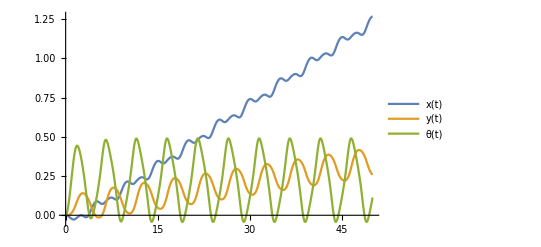

```mathematica
Plot[Evaluate[{x[t], y[t], θ[t]} /. solutionControl], {t, 0, duration},PlotLegends->{x[t],y[t],θ[t]}]
```

```mathematica
movieFrame[time_]:=Show[{body,head,tail,tailPivotLine1,tailPivotDot,tailPivotLine2,headPivotDot,headPivotLine1,headPivotLine2}/.robotParameters/.shapeChange/.solutionControl/.t-> time,PlotRange-> {{-(6 b + gap + 2) , 6 b + gap + 2}, {-(6 b + gap + 2) , 6 b + gap + 2}} /. robotParameters];
```

```mathematica
numberOfFrames = 300;
```

```mathematica
movieFrames = Table[movieFrame[k],{k,0,duration,duration/numberOfFrames}];
```

```mathematica
ListAnimate[movieFrames];
```

```mathematica
FL = {D[L,x'[t]],D[L,y'[t]],D[L,θ'[t]],D[L,ϕ'[t]],D[L,θ1'[t]]};
```

We define the momentum map by <J(v_q),η> which equals <FL(v_q),η_Q(q)>

```mathematica
J1 = (FL.ζQ)/ζ1/.{ζ2-> 0,ζ3-> 0};
```

```mathematica
J2 = (FL.ζQ)/ζ2/.{ζ1-> 0,ζ3-> 0};
```

```mathematica
J3 = (FL.ζQ)/ζ3/.{ζ2-> 0,ζ1-> 0};
```

```mathematica
testCase1={θ[t]-> 0, ϕ[t]-> 0, θ1[t]-> 0,θ'[t]-> 0, ϕ'[t]-> 0, θ1'[t]-> 0};
```

```mathematica
J1/.testCase1
```

3 mLong x'[t]

```mathematica
J2/.testCase1
```

3 mLat y'[t]

```mathematica
J3/.testCase1//FullSimplify
```

-3 mLong y[t] x'[t]+3 mLat x[t] y'[t]

```mathematica
testCase2 = {θ[t]-> 0, ϕ[t]-> 0, x'[t]-> 0, y'[t]-> 0, ϕ'[t]-> 0, θ1'[t]-> 0,θ1[t]-> 0};
```

```mathematica
J1/.testCase2
```

0

```mathematica
J2/.testCase2
```

0

```mathematica
J3/.testCase2//Simplify
```

(8 b^2 mLat+16 b gap mLat+8 gap^2 mLat+3 mRot) θ'[t]

```mathematica
testCase2Verification = (mRot+2 (mRot + mLat (2 b + 2 gap )^2)) θ'[t];
```

```mathematica
Simplify[(J3/.testCase2)-testCase2Verification]
```

0

Everything so far is commensurate with Scott’s analysis of a similar 3-link swimmer. Let’s get to the good stuff. We will, as per Scott’s analysis, need the locked inertia tensor, the connection form, and the local connection form.

```mathematica
rightpairing = λQ.FL/.{x'[t]-> ζQ[[1]],y'[t]-> ζQ[[2]],θ'[t]-> ζQ[[3]],ϕ'[t]-> ζQ[[4]],θ1'[t]-> ζQ[[5]]};
```

```mathematica
lockedInertiaTensor = {{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ2-> 0,λ3-> 0})/(ζ1 λ1),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ2-> 0,λ3-> 0})/(ζ2 λ1),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ2-> 0,λ3-> 0})/(ζ3 λ1)},{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ1-> 0,λ3-> 0})/(ζ1 λ2),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ1-> 0,λ3-> 0})/(ζ2 λ2),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ1-> 0,λ3-> 0})/(ζ3 λ2)},{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ2-> 0,λ1-> 0})/(ζ1 λ3),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ2-> 0,λ1-> 0})/(ζ2 λ3),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ1-> 0,λ2-> 0})/(ζ3 λ3)}};
```

```mathematica
Γ=Inverse[lit].{J1,J2,J3};
```

```mathematica
Adg = {{Cos[θ[t]],-Sin[θ[t]],y[t]},{Sin[θ[t]],Cos[θ[t]],-x[t]},{0,0,1}};
```

```mathematica
localLIT = Transpose[Adg].lockedInertiaTensor.Adg;
```

The following verification checks out when the joint angles are zero. Huzzah!

```mathematica
localLIT/.{ϕ[t]-> 0,θ1[t]-> 0}//Simplify//MatrixForm
```

(3 mLong | 0 | 0
0 | 3 mLat | 0
0 | 0 | 8 b^2 mLat+16 b gap mLat+8 gap^2 mLat+3 mRot)

```mathematica
SE2BV = {x'[t] Cos[θ[t]] + y'[t] Sin[θ[t]], y'[t] Cos[θ[t]] -x'[t] Sin[θ[t]], θ'[t]};
```

A mechanical connection is given by Γ=A(r) rdot + g^-1 gdot=A(r) rdot + SE2BV

```mathematica
g = {{Cos[θ[t]],-Sin[θ[t]], x[t]},{Sin[θ[t]],Cos[θ[t]], y[t]},{0,0,1}};
```

```mathematica
Inverse[g].D[g,t]//FullSimplify//MatrixForm
```

(0 | -θ'[t] | Cos[θ[t]] x'[t]+Sin[θ[t]] y'[t]
θ'[t] | 0 | -Sin[θ[t]] x'[t]+Cos[θ[t]] y'[t]
0 | 0 | 0)

Okay, great. Just wanted to check my understanding of how we represent the body velocity. I now recall that we represent the above matrix as a 3x1 vector.

```mathematica
A = Inverse[Adg].Γ - SE2BV;
```

Much like Scott’s approach to finding the local connection form, I will not wait for Mathematica to simplify A. How can I exploit what I know A should look like so as to require less from Mathematica computationally?

## Q-learning for Varying Stiffness and Amplitude

We want to determine the optimal way to vary the stiffness of a spring in the three-link swimmer over some specified number of cycles. This seems like a good starting point. We can then add the amplitude variation after successfully optimizing the spring stiffness.

```mathematica
PEtailk = 1/2 k1 θ1[t]^2;
```

```mathematica
Lk = KEbody+KEhead+KEtail-PEtailk;
```

```mathematica
xodek = D[D[Lk,x'[t]],t]-D[Lk,x[t]]==0;
```

```mathematica
yodek = D[D[Lk,y'[t]],t]-D[Lk,y[t]]==0;
```

```mathematica
θodek = D[D[Lk,θ'[t]],t]-D[Lk,θ[t]]==0;
```

```mathematica
θ1odek = D[D[Lk,θ1'[t]],t]-D[Lk,θ1[t]]==-c1 θ1'[t];
```

```mathematica
ϕodek = D[D[Lk,ϕ'[t]],t]-D[Lk,ϕ[t]]==0;
```

```mathematica
odesk ={xodek,yodek,θodek,θ1odek,ϕodek};
```

Some functions we will need to define are QUpdate[saPair_, reward_, currentQ_], Reward[state], and sol(defined above). I should first define the learning problem. What is the environment, agent, etc.?

PSEUDOCODE

Establish Q matrix, states, and actions.
Define terminal state

Start a loop:
	Initialize state
	Start another loop:
		Choose the action based on the policy
		Take action, observe reward and next state
		Update Q function
		Update state
	until S is terminal

```mathematica
rlmodel=-Graphics-;
```

```mathematica
rlmodel
```

-Graphics-

Define the reward to be how far the robot moved in the x direction for that cycle. States are x (or omit x), θ, ϕ, θ1, and d/dt θ1. Actions are choices of amplitude and spring stiffness throughout a cycle. Define an episode to be n cycles of a sinusoidal signal. Vary amplitude and stiffness throughout that episode.

Define learning rate, discount factor, time step

```mathematica
(*θstates = Range[0.0,2π,π/20];
θ1states=Range[0.0,2π,π/20];
ϕstates=Range[0.0,2 π,0.10];
θ1dotstates=Range[-π/2,π/2,π/20];
ϕdotAction=Range[-0.4,0.4,1/20];
stiffnessAction=Range[0.5,2.0,1/2];*)
```

```mathematica
α=0.9;
```

```mathematica
γ=0.90;
```

```mathematica
δt=1;
```

```mathematica
eps=0.6;
```

Here are some interesting facts to keep in mind when troubleshooting the issue involving incorrect ϕ[t] solutions resulting from NDSolve:

There is a small range of ϕ’[t]s that we can prescribe without NDSolve breaking. This range appears to be somewhere around -0.2 to 0.2. The following error is thrown for larger ranges: “Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions”

In this range, solutions for ϕ[t] seem to increase without bound. The final element in each of these lists is phi[t] from NDSolve. 

{0.,0.,0.,1.}
{0.0162309,0.0139078,0.01081,1.98311}
{0.0509463,0.0238074,0.000624716,2.98269}
{0.0816645,0.0112192,-0.0239709,3.98613}
{0.0862345,-0.0168392,-0.0273199,4.99539}
{0.0678275,-0.0319941,0.0014191,5.99936}
{0.0531459,-0.0154013,0.0274443,6.9898}
{0.0444197,0.000761138,0.00366238,7.97547}
{0.0298581,0.000712483,-0.000260418,8.97364}
{0.0130209,-0.00214751,-0.00864277,9.90534}
New episode
{0.00584727,0.00645897,0.0123996,0.993729}
{0.0296805,0.0172183,0.00812076,1.99331}

ϕ’[t] from NDSolve is constant and most of the time 1 rad/s which isn’t ever what is prescribed.

```mathematica
Reward[currentSol_,pastSol_]:=currentSol-pastSol;
```

```mathematica
QUpdate[newPos_,oldPos_,actionPos_,reward_,Q_]:=Q[[oldPos[[1]],oldPos[[2]],oldPos[[3]],oldPos[[4]],actionPos[[1]],actionPos[[2]]]]+α (reward+γ Max[ Q[[newPos[[1]],newPos[[2]],newPos[[3]],newPos[[4]]]]]-Q[[oldPos[[1]],oldPos[[2]],oldPos[[3]],oldPos[[4]],actionPos[[1]],actionPos[[2]]]]);
```

```mathematica
getActionPos[action_]:={Position[stiffnessAction,action[[1]]][[1]][[1]],Position[ϕdotAction,action[[2]]][[1]][[1]]};
```

We could define an epsilon that decays as the number of episodes increases.

```mathematica
getMaxPos[state_,Q_]:=Position[Q[[state[[1]],state[[2]],state[[3]],state[[4]]]],Max[Q[[state[[1]],state[[2]],state[[3]],state[[4]]]]]][[1]];
```

```mathematica
chooseAction[eps_,state_,Q_]:= If[eps>Random[],action={RandomChoice[stiffnessAction],RandomChoice[ϕdotAction]},action={stiffnessAction[[getMaxPos[state,Q][[1]]]],ϕdotAction[[getMaxPos[state,Q][[2]]]]}];
```

```mathematica
takeAction[action_,initialCon_,time_]:=NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> action[[1]]}/.{ϕ'[t]-> action[[2]]}/.{ρ-> 1000}/.robotParameters,initialCon},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,time, time+δt},Method->{"EquationSimplification"-> "Residual"}];
```

```mathematica
numOfEpisodes = 10;
```

```mathematica
lengthOfEpisode=10;
```

```mathematica
getStatePos[state_]:={Position[states,state[[1]]][[1]],Position[states,state[[2]]][[1]],Position[states,state[[3]]][[1]],Position[states,state[[4]]][[1]]};
```

```mathematica
getClosestStatePos[states_,newState_]:={Position[states[[1]],Nearest[states[[1]],newState[[1]]][[1]]][[1,1]],Position[states[[2]],Nearest[states[[2]],newState[[2]]][[1]]][[1,1]],Position[states[[3]],Nearest[states[[3]],newState[[3]]][[1]]][[1,1]],Position[states[[4]],Nearest[states[[4]],newState[[4]]][[1]]][[1,1]]};
```

```mathematica
getInitialPos[state1_,state2_,state3_,state4_]:={Position[state1,0.][[1]][[1]],Position[state2,0.][[1]][[1]],Position[state3,0][[1]][[1]],Position[state4,0.][[1]][[1]]};
```

```mathematica
(*Initialize Q matrix, states, actions, and terminal state (defined as the maximum time one can wander through the state space)*)
θstates = Range[0.0,2π,π/20];
θ1states=Range[0.0,2π,π/20];
ϕstates=Range[0.0,2 π,π/20];
θ1dotstates=Range[-π/2,π/2,π/20];
ϕdotAction=Range[-0.2,0.2,1/10];
stiffnessAction=Range[0.5,2.0,1/2];
states={θstates,θ1states,θ1dotstates,ϕstates};
Q=Table[0.0,{s1,1,Length[θstates]},{s2,1,Length[θ1states]},{s3,1,Length[θ1dotstates]},{s4,1,Length[ϕstates]},{a1,1,Length[stiffnessAction]},{a2,1,Length[ϕdotAction]}];
(*Run a series of episodes*)
For[i=1, i≤ numOfEpisodes, i++,initialConditions={x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0,ϕ[0]==0};
(*Initialize*)
statePos=getInitialPos[θstates,θ1states,θ1dotstates,ϕstates]; pastx=0;
(*Take "lengthOfEpisode" steps in the environment*)
For[j=0, j<lengthOfEpisode, j++,
(*Choose the action from current state using desired policy*)
action=chooseAction[eps,statePos,Q];actionPos=getActionPos[action];
(*Print[action];*)
 (*Take action and observe distance in x direction (reward)*)
solution=takeAction[action,initialConditions,j];
newx=((x[t]/.solution)/.{t-> (j+δt)})[[1]];
(*Observe new state*)
newState=(({θ[t],θ1[t],θ1'[t],ϕ[t]}/.solution)/.{t-> j+δt})[[1]];
(*Print[newState];*)
(*Use Mod[anglestates,2pi]*)
newState={Mod[newState[[1]],2 π],Mod[newState[[2]],2 π],newState[[3]],Mod[newState[[4]],2 π]};
(*Determine which discretized state newState is closest to. Really this finds the closest position in the set of states and returns it so it can be matched in the Q matrix.*)
newStatePos=getClosestStatePos[states,newState];
(*Compute reward and update previous x position*)
r=Reward[newx,pastx];
pastx=newx;
(*Update Q matrix. Be sure to add Q[currentstate]=QUpdate*)
Q[[statePos[[1]],statePos[[2]],statePos[[3]],statePos[[4]],actionPos[[1]],actionPos[[2]]]]=QUpdate[newStatePos,statePos,actionPos,r,Q];
statePos=newStatePos;
initialConditions=(({x[j+δt]==x[t],y[j+δt]==y[t],θ[j+δt]== θ[t],x'[j+δt]==x'[t],y'[j+δt]==y'[t],θ'[j+δt]==θ'[t],θ1[j+δt]==θ1[t],θ1'[j+δt]==θ1'[t],ϕ[j+δt]==ϕ[t]}/.solution)/.{t->j+δt})[[1]]]]
```

```mathematica
Qfinal=Q;
```

```mathematica
Max[Q]
```

0.033044

Policy Extraction and Simulation

```mathematica
policyMatrix=Table[{0.0, 0.0},{s1,1,Length[θstates]},{s2,1,Length[θ1states]},{s3,1,Length[θ1dotstates]},{s4,1,Length[ϕstates]}];
```

```mathematica
(*For[s1=1,s1≤ Length[θstates],s1++,
For[s2=1,s2≤ Length[θ1states],s2++,
For[s3=1,s3≤ Length[θ1dotstates],s3++,
For[s4=1,s4≤ Length[ϕstates],s4++,
policyMatrix[[s1,s2,s3,s4]]={stiffnessAction[[getMaxPos[{s1,s2,s3,s4},Qfinal][[1]]]],ϕdotAction[[getMaxPos[{s1,s2,s3,s4},Qfinal][[2]]]]}]]]]*)
```

```mathematica
policyMatrix;
```

```mathematica
statePos=getInitialPos[θstates,θ1states,θ1dotstates,ϕstates];
initialConditions={x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0,ϕ[0]==0};
listOfSol={};
listOfPlots={};
listOfActionPlots={};
listOfPhiPlots={};
listOfPhiDotPlots={};
listOfActions={};
For[time=0,time<lengthOfEpisode,time++,
(*Use an epsilon of zero in the chooseAction function (act entirely greedy)*)
action=chooseAction[0.0,statePos,Qfinal];
AppendTo[listOfActions,action];
solutionFinal=takeAction[action,initialConditions,time];
newState=(({θ[t],θ1[t],θ1'[t],ϕ[t]}/.solutionFinal)/.{t-> time+δt})[[1]];
(*Use Mod[anglestates,2pi]*)
newState={Mod[newState[[1]],2 π],Mod[newState[[2]],2π],newState[[3]],Mod[newState[[4]],2 π]};
(*Determine which discretized state newState is closest to.*)
newStatePos=getClosestStatePos[states,newState];
statePos=newStatePos;
(*Generate a plot for the state and action over δt*)
AppendTo[listOfSol,solutionFinal];
If[time==0,plotState=Plot[Evaluate[{x[t], y[t], θ[t]}/.solutionFinal], {t,time,time+δt},PlotLegends-> {x[t],y[t],θ[t]},PlotStyle->{Blue,Green,Red}],plotState=Plot[Evaluate[{x[t], y[t], θ[t]} /.solutionFinal], {t,time,time+δt},PlotStyle->{Blue,Green,Red}]];
AppendTo[listOfPlots,plotState];
If[time==0,ϕPlot=Plot[Evaluate[ϕ[t]/.solutionFinal], {t,time,time+δt},PlotLegends-> {ϕ[t]},PlotStyle->Blue],ϕPlot=Plot[Evaluate[ϕ[t]/.solutionFinal], {t,time,time+δt},PlotStyle->Blue]];
AppendTo[listOfPhiPlots,ϕPlot];
If[time==0,ϕDotPlot=Plot[Evaluate[ϕ'[t]/.solutionFinal], {t,time,time+δt},PlotLegends-> {ϕ'[t]},PlotRange->{-0.2,0.2},PlotStyle->Blue],ϕDotPlot=Plot[Evaluate[ϕ'[t]/.solutionFinal], {t,time,time+δt},PlotStyle->Blue]];
AppendTo[listOfPhiDotPlots,ϕDotPlot];If[time==0,plotAction=Plot[action,{t,time,time+δt},PlotLegends->{k1[t],ϕ'[t]},PlotStyle->{Cyan,Magenta}],plotAction=Plot[action, {t, time, time+δt},PlotStyle->{Cyan,Magenta}]];
AppendTo[listOfActionPlots,plotAction];
initialConditions=(({x[time+δt]==x[t],y[time+δt]==y[t],θ[time+δt]== θ[t],x'[time+δt]==x'[t],y'[time+δt]==y'[t],θ'[time+δt]==θ'[t],θ1[time+δt]==θ1[t],θ1'[time+δt]==θ1'[t],ϕ[time+δt]==ϕ[t]}/.solutionFinal)/.{t->time+δt})[[1]]]
```

```mathematica
solutionFinal[[1,9]]
```

ϕ[t]→InterpolatingFunction[{{9., 10.}}, <>][t]

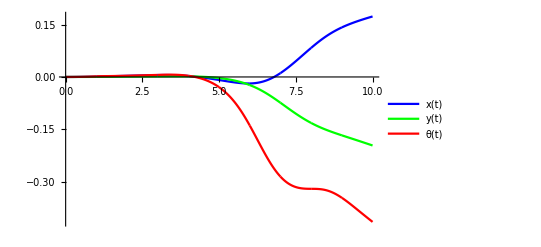

```mathematica
Show[listOfPlots,PlotRange-> All]
```

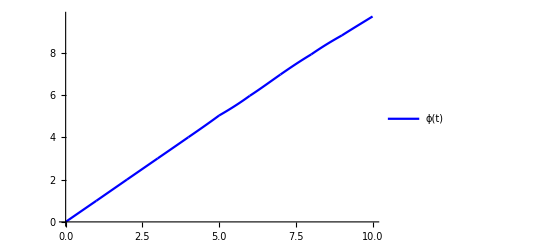

```mathematica
Show[listOfPhiPlots,PlotRange-> All]
```

ϕ should never be greater than 2π. I’ve yet to implement solving for phi directly rather than using NDSolve, but they should both be the same.

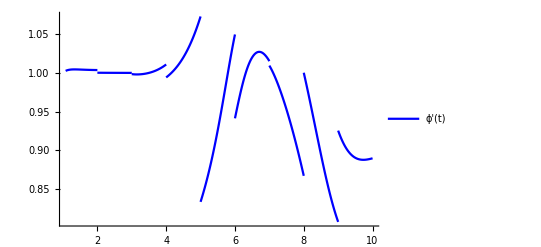

```mathematica
Show[listOfPhiDotPlots,PlotRange-> All]
```

The above plot is of ϕ’[t] as solved by NDSolve. This explains why the result is the Exorcist gait, but this shouldn’t be...
Does it make sense to solve for phi’[t] given that we prescribe it? We can compute the resulting phi[t], so does it make sense to solve for phi[t]? The more I think about it the more I’m convinced it isn’t. Even if it doesn’t make sense to use NDSolve to find ϕ[t], it should still result in what we can compute manually.

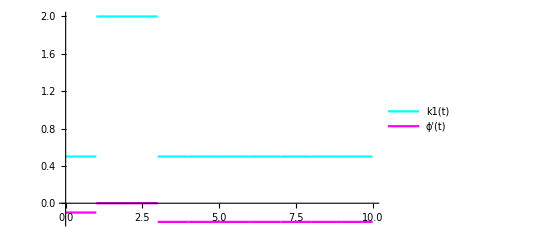

```mathematica
Show[listOfActionPlots,PlotRange-> All]
```

Hmmmm, I suspect a bug...actions aren’t changing over the rest of the episode’s duration...

```mathematica
movieFrameQ[time_,step_]:=Show[{body,head,tail,tailPivotLine1,tailPivotDot,tailPivotLine2,headPivotDot,headPivotLine1,headPivotLine2}/.robotParameters/.listOfSol[[step]]/.{t-> time},PlotRange-> {{-(6 b + gap) , 6 b + gap}, {-(6 b + gap ) , 6 b + gap }} /. robotParameters];
```

```mathematica
numberOfFrames = 100;
```

```mathematica
movieFrames=Table[Table[movieFrameQ[k,j],{k,j-1,j,δt/numberOfFrames}],{j,1,lengthOfEpisode}];
```

```mathematica
movieFrames=Flatten[movieFrames];
```

```mathematica
ListAnimate[movieFrames]
```